70.0826

66.8482

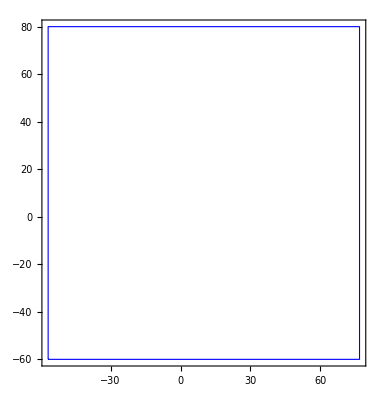

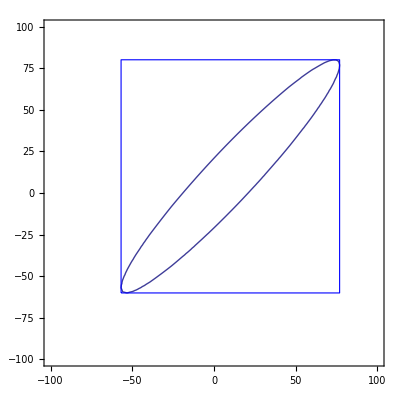

```mathematica
invsigmadl = 1/(63^2);
invsigmaz = 1/(10^2);
angle = 1.57/2;

a=(((4.0)/(Cos[angle]^ 2))*invsigmadl)+((2*(Tan[angle]^2)*invsigmaz));
b=-4*Tan[angle]*invsigmaz;
c=2*invsigmaz;
b2=(b/2)*(b/2);

bby=3/Sqrt[c-(b2/a)]

bbz=3/Sqrt[a-(b2/c)]


y0 = 10;
z0 = 10;



k = ContourPlot[(((a*((y0 - dy)*(y0 -dy)))+(b*(y0 -dy)*(z0 -dz))+(c*((z0 -dz)*(z0 -dz)))))==9,{dy,-100,100},{dz,-100,100}];

p2 = Graphics[{EdgeForm[{Thick,Blue}],FaceForm[],Rectangle[{z0-bbz,y0-bby},{z0+bbz,y0+bby}]},Frame->True]

p1 = Graphics[k];

Show[p1,p2]
```